```mathematica
angle=Import["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/Theta.dat"];
spindata=Import["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/SpinSTMi.dat"];
```

```mathematica
spin=ArrayReshape[spindata,{200*200,2,3}];
spinformatted=Table[{spin[[n,1]]-spin[[n,2]]/2,spin[[n,1]]+spin[[n,2]]/2},{n,1,200*200}];
theta2=angle[[100*100+1;;100*100*2,{1,2,4}]];
theta1=angle[[1;;100*100,{1,2,4}]];
phi=angle[[All,{1,2,5}]];
```

```mathematica
Graph of the spins
```

```mathematica
Graphics3D[{Thickness[Medium],Arrowheads[Small],Arrow[spinformatted]},Axes->False,Boxed->False]
```

```mathematica
Graph of the profile (data brute)
```

```mathematica
ListPlot3D[{theta1,theta2},PlotRange->All]
```

```mathematica
maxtheta1=Max[theta1[[All,3]]];
maxtheta2=Max[theta2[[All,3]]];
Position[theta1,maxtheta1]
Position[theta2,maxtheta2]
```

{{7120,3}}

{{7120,3}}

```mathematica
rtheta1=Sort[Table[{Norm[theta1[[7120,{1,2}]]-theta1[[i,{1,2}]]]*0.27,theta1[[i,3]]},{i,1,100*100}],#1[[1]]<#2[[1]]&];
rtheta2=Sort[Table[{Norm[theta1[[7120,{1,2}]]-theta2[[i,{1,2}]]]*0.27,theta2[[i,3]]},{i,1,100*100}],#1[[1]]<#2[[1]]&];
```

```mathematica
ListPlot[{rtheta1,rtheta2},PlotRange->{{-0.05,3.5},{0,Pi}},PlotStyle->{PointSize[0.02]},PlotLegends->{"layer 1","layer 2"},PlotMarkers->Automatic,FrameLabel->{"r (nm)","θ (rad)"},LabelStyle->Directive[Bold,Thick,Large],Frame->True,FrameStyle->Directive[Medium]]
```

```mathematica
Graph of the profile (Mean data)
```

```mathematica
end=100*99;i=2;
Clear[avetheta1];avetheta1={{rtheta1[[1,1]],rtheta1[[1,2]],0}};
While[i<end+1,
n=0;j=0;
While[Abs[rtheta1[[i+j,1]]-rtheta1[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[avetheta1,{rtheta1[[i,1]],Mean[rtheta1[[i;;i+n-1,2]]],Sqrt[Total[(Mean[rtheta1[[i;;i+n-1,2]]]-rtheta1[[i;;i+n-1,2]])^2]/n]}];i=i+n,AppendTo[avetheta1,{rtheta1[[i,1]],rtheta1[[i,2]],0}];i=i+1];
]
```

```mathematica
end=100*99;i=4;
Clear[avetheta2];avetheta2={{rtheta2[[1,1]],Mean[rtheta2[[1;;3,2]]],Sqrt[Total[(Mean[rtheta2[[1;;3,2]]]-rtheta2[[1;;3,2]])^2]/3]}};
While[i<end+1,
n=0;j=0;
While[Abs[rtheta2[[i+j,1]]-rtheta2[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[avetheta2,{rtheta2[[i,1]],Mean[rtheta2[[i;;i+n-1,2]]],Sqrt[Total[(Mean[rtheta2[[i;;i+n-1,2]]]-rtheta2[[i;;i+n-1,2]])^2]/n]}];i=i+n,AppendTo[avetheta2,{rtheta2[[i,1]],rtheta2[[i,2]],0}];i=i+1];
]
```

```mathematica
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_theta/profile_theta1.dat",avetheta1,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_theta/profile_theta2.dat",avetheta2,"Table"];
```

```mathematica
plot=ListPlot[{avetheta1,avetheta2},PlotMarkers->{Automatic,Large},PlotRange->{{-0.01,3.5},{0,Pi}},PlotLegends->Placed[{"layer 1","layer 2"},{0.5,0.5}],FrameLabel->{Style["r (nm)",FontSize->30],Style["θ (rad)",FontSize->30]},BaseStyle->{FontSize->26},LabelStyle->Directive[Bold,Thick,Large],Frame->True,FrameStyle->Directive[Medium,FontSize->30],ImageSize->1000];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/4T/profile/profile.pdf",plot,"pdf"];
```

```mathematica
Graph of the profile as contour (Mean data)
```

```mathematica
ListContourPlot[{theta1,theta2},PlotRange->{{37,53},{37,53},All},LabelStyle->Directive[Bold,Thick,Large],Frame->False,FrameStyle->Directive[Medium],PlotLegends->Automatic,InterpolationOrder->3,ContourLabels->False,ContourStyle->Directive[Dashed],Contours->10]
```

```mathematica
Graph of the profile and the Energy density(Mean data)
```

```mathematica
Energy1=Import["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/Energy_l1.dat"];
Energy2=Import["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/Energy_l2.dat"];
```

```mathematica
Exchange Energy
```

```mathematica
Exch1=Table[{(Energy1[[i,1]]-angle[[7120,1]])*0.27,(Energy1[[i,2]]-angle[[7120,2]])*0.27,(Energy1[[i,3]]-Energy1[[1,3]])*1000.0},{i,1,100*100}];
Exch2=Table[{(Energy2[[i,1]]-angle[[7120,1]])*0.27,(Energy2[[i,2]]-angle[[7120,2]])*0.27,(Energy2[[i,3]]-Energy2[[1,3]])*1000.0},{i,1,100*100}];
```

```mathematica
rExch1=Sort[Table[{Norm[Exch1[[i,{1,2}]]],Exch1[[i,3]]},{i,1,100*100}],#1[[1]]<#2[[1]]&];
rExch2=Sort[Table[{Norm[Exch2[[i,{1,2}]]],Exch2[[i,3]]},{i,1,100*100}],#1[[1]]<#2[[1]]&];
```

```mathematica
end=100*99;i=2;
Clear[aveExch1];
aveExch1={{rExch1[[1,1]],rExch1[[1,2]],0}};
While[i<end+1,
n=0;j=0;
While[Abs[rExch1[[i+j,1]]-rExch1[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[aveExch1,{rExch1[[i,1]],Mean[rExch1[[i;;i+n-1,2]]],Sqrt[Total[(Mean[rExch1[[i;;i+n-1,2]]]-rExch1[[i;;i+n-1,2]])^2]/n]}];i=i+n,AppendTo[aveExch1,{rExch1[[i,1]],rExch1[[i,2]],0}];i=i+1];
]
```

```mathematica
end=100*99;i=4;
Clear[aveExch2];aveExch2={{rExch2[[1,1]],Mean[rExch2[[1;;3,2]]],Sqrt[Total[(Mean[rExch2[[1;;3,2]]]-rExch2[[1;;3,2]])^2]/3]}};
While[i<end+1,
n=0;j=0;
While[Abs[rExch2[[i+j,1]]-rExch2[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[aveExch2,{rExch2[[i,1]],Mean[rExch2[[i;;i+n-1,2]]],Sqrt[Total[(Mean[rExch2[[i;;i+n-1,2]]]-rExch2[[i;;i+n-1,2]])^2]/n]}];i=i+n,AppendTo[aveExch2,{rExch2[[i,1]],rExch2[[i,2]],0}];i=i+1];
]
```

```mathematica
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Exch/profile_Exch1.dat",aveExch1,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Exch/profile_Exch2.dat",aveExch2,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Exch/Exch1.dat",Exch1,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Exch/Exch2.dat",Exch2,"Table"];
```

```mathematica
legendexch=Labeled[ContourPlot[y,{x,0,1/6},{y,-1,1},ContourStyle->None,Frame->True,
Contours->100,ColorFunction->ColorData["Temperature"],ColorFunctionScaling->True,AspectRatio->10,PlotRange->All,FrameTicks->{{Flatten[{Table[{j,,{0.2,0}},{j,-1,1,0.5}],Table[{j,,{0.1,0}},{j,-1,1,0.1}]},1],Flatten[{Table[{j,j,{0.2,0}},{j,-1,1,0.5}],Table[{j,,{0.1,0}},{j,-1,1,0.1}]},1]},{None,None}},FrameTicksStyle->Directive[Bold,FontSize->50],FrameStyle->Directive[Thickness[0.05],FontSize->50],ImageSize->270,ImagePadding->{{100,100},{30,30}}],Rotate[Style["Energy (meV)",Bold,FontSize->70],Pi/2],Right];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/4T/profile/legend_exch.pdf",legendexch,"pdf"];
```

```mathematica
plotExch1=ListContourPlot[Exch1,PlotRange->{{-10,10}*0.27,{-10,10}*0.27,All},LabelStyle->Directive[Bold,Thick,Large],Frame->True,ColorFunction->ColorData[{"Temperature",{-1,1}}],ColorFunctionScaling->False,

FrameTicks->{{Flatten[{Table[{j,j,{0.02,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],0.2}]},1],
Flatten[{Table[{j,,{0.02,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],0.2}]},1]},



{Flatten[{Table[{j,,{0.02,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],0.2}]},1],Flatten[{Table[{j,j,{0.02,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],0.2}]},1]}}

,FrameTicksStyle->Directive[Bold,FontSize->50],InterpolationOrder->3,ContourLabels->False,ContourStyle->Directive[Thickness[0.001]],Contours->20,FrameLabel->None,FrameStyle->Directive[Thickness[0.005]],ImageSize->1000,ImagePadding->100,PlotLegends->Placed[Style["Exchange Fe@Ir",Bold,FontSize->70,Background->White],{0.5,0.1}]];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/4T/profile/Exchl1.pdf",plotExch1,"pdf"];
```

```mathematica
plotExch2=ListContourPlot[Exch2,PlotRange->{{-10,10}*0.27,{-10,10}*0.27,All},LabelStyle->Directive[Bold,Thick,Large],Frame->True,ColorFunction->ColorData[{"Temperature",{-1,1}}],ColorFunctionScaling->False,FrameTicks->

{{Flatten[{Table[{j,,{0.02,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],0.2}]},1],
Flatten[{Table[{j,,{0.02,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],0.2}]},1]},



{Flatten[{Table[{j,,{0.02,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],0.2}]},1],Flatten[{Table[{j,j,{0.02,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],0.2}]},1]}}

,InterpolationOrder->3,ContourLabels->False,ContourStyle->Directive[Thickness[0.001]],Contours->20,FrameLabel->None,FrameStyle->Directive[Thickness[0.005],FontSize->50],ImageSize->1000,ImagePadding->100,PlotLegends->Placed[Style["Exchange Fe@Pd",Bold,FontSize->70,Background->White],{0.5,0.1}]];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/4T/profile/Exchl2.pdf",plotExch2,"pdf"];
```

```mathematica
mapExch=ListPlot3D[Exch,PlotRange->{{35,55},{35,55},All},PlotStyle->Opacity[0.9], Mesh -> None,TicksStyle->Directive[Bold,12]];
spins=Graphics3D[{Thickness[Medium],Arrowheads[Small],PlotRange->{{35,55},{35,55},All},Arrow[spinformatted]},Axes->False,Boxed->False];
graph=Show[{spins,mapExch},ImageSize->100,TicksStyle->Directive[Bold,12],PlotRange->{{35,55},{35,55},All},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->False,ViewPoint->Top];
```

```mathematica
ListPlot3D[Exch,PlotRange->{{35,55},{35,55},All},PlotStyle->Opacity[0.9], Mesh -> None,TicksStyle->Directive[Bold,12]]
```

```mathematica
DM Energy
```

```mathematica
EDM=Table[{Energy1[[i,1]],angle[[i,2]],(Energy1[[i,6]])*1000.0},{i,1,100*100}];
EDM2=Table[{Energy2[[i,1]],angle[[i,2]],(Energy2[[i,6]])*1000.0},{i,1,100*100}];
```

```mathematica
EDM1=Table[{(Energy1[[i,1]]-angle[[7120,1]])*0.27,(Energy1[[i,2]]-angle[[7120,2]])*0.27,(Energy1[[i,6]]-Energy1[[1,6]])*1000.0},{i,1,100*100}];
EDM2=Table[{(Energy2[[i,1]]-angle[[7120,1]])*0.27,(Energy2[[i,2]]-angle[[7120,2]])*0.27,(Energy2[[i,6]]-Energy2[[1,6]])*1000.0},{i,1,100*100}];
```

```mathematica
rEDM1=Sort[Table[{Norm[EDM1[[i,{1,2}]]],EDM1[[i,3]]},{i,1,100*100}],#1[[1]]<#2[[1]]&];
rEDM2=Sort[Table[{Norm[EDM2[[i,{1,2}]]],EDM2[[i,3]]},{i,1,100*100}],#1[[1]]<#2[[1]]&];
```

```mathematica
end=100*99;i=2;
Clear[aveEDM1];
aveEDM1={{rEDM1[[1,1]],rEDM1[[1,2]],0}};
While[i<end+1,
n=0;j=0;
While[Abs[rEDM1[[i+j,1]]-rEDM1[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[aveEDM1,{rEDM1[[i,1]],Mean[rEDM1[[i;;i+n-1,2]]],Sqrt[Total[(Mean[rEDM1[[i;;i+n-1,2]]]-rEDM1[[i;;i+n-1,2]])^2]/n]}];i=i+n,AppendTo[aveEDM1,{rEDM1[[i,1]],rEDM1[[i,2]],0}];i=i+1];
]
```

```mathematica
end=100*99;i=4;
Clear[aveEDM2];
aveEDM2={{rEDM2[[1,1]],Mean[rEDM2[[1;;3,2]]],Sqrt[Total[(Mean[rEDM2[[1;;3,2]]]-rEDM2[[1;;3,2]])^2]/3]}};
While[i<end+1,
n=0;j=0;
While[Abs[rEDM2[[i+j,1]]-rEDM2[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[aveEDM2,{rEDM2[[i,1]],Mean[rEDM2[[i;;i+n-1,2]]],Sqrt[Total[(Mean[rEDM2[[i;;i+n-1,2]]]-rEDM2[[i;;i+n-1,2]])^2]/n]}];i=i+n,AppendTo[aveEDM2,{rEDM2[[i,1]],rEDM2[[i,2]],0}];i=i+1];
]
```

```mathematica
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Edm/profile_Edm1.dat",aveEDM1,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Edm/profile_Edm2.dat",aveEDM2,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Edm/Edm1.dat",EDM1,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Edm/Edm2.dat",EDM2,"Table"];
```

```mathematica
plot=ListContourPlot[EDM,PlotRange->{{35,55},{35,55},All},LabelStyle->Directive[Bold,Thick,Large],Frame->True,PlotLegends->Automatic,InterpolationOrder->3,ContourLabels->False,ContourStyle->Directive[Dashed],Contours->10,FrameLabel->"DM Energy of layer 1 (meV)"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/4T/profile/DM.pdf",plot,"pdf"];
```

```mathematica
ListContourPlot[EDM2,PlotRange->{{35,55},{35,55},All},LabelStyle->Directive[Bold,Thick,Large],Frame->True,PlotLegends->Automatic,InterpolationOrder->3,ContourLabels->False,ContourStyle->Directive[Dashed],Contours->10,FrameLabel->"DM Energy of layer 2 (meV)"]
```

```mathematica
ListPlot3D[EDM,PlotRange->{{35,55},{35,55},All},PlotStyle->Opacity[0.9], Mesh -> None,TicksStyle->Directive[Bold,12]]
```

```mathematica
Total Energy
```

```mathematica
totE1=Table[{(Energy1[[i,1]]-angle[[7120,1]])*0.27,(Energy1[[i,2]]-angle[[7120,2]])*0.27,(Energy1[[i,10]]-Energy1[[1,10]])*1000.0},{i,1,100*100}];
totE2=Table[{(Energy2[[i,1]]-angle[[7120,1]])*0.27,(Energy2[[i,2]]-angle[[7120,2]])*0.27,(Energy2[[i,10]]-Energy2[[1,10]])*1000.0},{i,1,100*100}];
```

```mathematica
rtotE1=Sort[Table[{Norm[totE1[[i,{1,2}]]],totE1[[i,3]]},{i,1,100*100}],#1[[1]]<#2[[1]]&];
rtotE2=Sort[Table[{Norm[totE2[[i,{1,2}]]],totE2[[i,3]]},{i,1,100*100}],#1[[1]]<#2[[1]]&];
end=100*99;i=2;
Clear[avetotE1];
avetotE1={{rtotE1[[1,1]],rtotE1[[1,2]],0}};
While[i<end+1,
n=0;j=0;
While[Abs[rtotE1[[i+j,1]]-rtotE1[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[avetotE1,{rExch1[[i,1]],Mean[rtotE1[[i;;i+n-1,2]]],Sqrt[Total[(Mean[rtotE1[[i;;i+n-1,2]]]-rtotE1[[i;;i+n-1,2]])^2]/n]}];i=i+n,AppendTo[avetotE1,{rtotE1[[i,1]],rtotE1[[i,2]],0}];i=i+1];
]
end=100*99;i=4;
Clear[avetotE2];avetotE2={{rtotE2[[1,1]],Mean[rtotE2[[1;;3,2]]],Sqrt[Total[(Mean[rtotE2[[1;;3,2]]]-rtotE2[[1;;3,2]])^2]/3]}};
While[i<end+1,
n=0;j=0;
While[Abs[rtotE2[[i+j,1]]-rtotE2[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[avetotE2,{rtotE2[[i,1]],Mean[rtotE2[[i;;i+n-1,2]]],Sqrt[Total[(Mean[rtotE2[[i;;i+n-1,2]]]-rtotE2[[i;;i+n-1,2]])^2]/n]}];i=i+n,AppendTo[avetotE2,{rtotE2[[i,1]],rtotE2[[i,2]],0}];i=i+1];
]
```

```mathematica
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Etot/profile_totE1.dat",avetotE1,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Etot/profile_totE2.dat",avetotE2,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Etot/totE1.dat",totE1,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Etot/totE2.dat",totE2,"Table"];
```

```mathematica
end=100*99;i=2;
sumrtotE1={{rtotE1[[1,1]],rtotE1[[1,2]]}};
While[i<end+1,
n=0;j=0;
While[Abs[rtotE1[[i+j,1]]-rtotE1[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[sumrtotE1,{rtotE1[[i,1]],Total[rtotE1[[1;;i+n-1,2]]]}];i=i+n,AppendTo[sumrtotE1,{rtotE1[[i,1]],Total[rtotE1[[1;;i,2]]]}];i=i+1];
]
end=100*99;i=4;
sumrtotE2={{rtotE2[[1,1]],Total[rtotE2[[1;;3,2]]]}};
While[i<end+1,
n=0;j=0;
While[Abs[rtotE2[[i+j,1]]-rtotE2[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[sumrtotE2,{rtotE2[[i,1]],Total[rtotE2[[1;;i+n-1,2]]]}];i=i+n,AppendTo[sumrtotE2,{rtotE2[[i,1]],Total[rtotE2[[1;;i,2]]]}];i=i+1];
]
```

```mathematica
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Etot/sumtotE1.dat",sumrtotE1,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Etot/sumtotE2.dat",sumrtotE2,"Table"];
```

```mathematica
plote1=ListContourPlot[totE1,PlotRange->{{-10,10}*0.27,{-10,10}*0.27,All},LabelStyle->Directive[Bold,Thick,Large],Frame->True,ColorFunction->ColorData[{"Temperature",{-3,3}}],ColorFunctionScaling->False,FrameTicks->

{{Flatten[{Table[{j,j,{0.02,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],0.2}]},1],
Flatten[{Table[{j,,{0.02,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,1]]]*0.27],Ceiling[Max[totEformat[[All,1]]]*0.27],0.2}]},1]},



{Flatten[{Table[{j,,{0.02,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],0.2}]},1],Flatten[{Table[{j,,{0.02,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],1}],Table[{j,,{0.01,0}},{j,Floor[Min[totEformat[[All,2]]]*0.27],Ceiling[Max[totEformat[[All,2]]]*0.27],0.2}]},1]}}

,InterpolationOrder->3,ContourLabels->False,ContourStyle->Directive[Thickness[0.001]],Contours->20,
FrameLabel->None,FrameStyle->Directive[Thickness[0.005],FontSize->50],ImageSize->1000,ImagePadding->100,PlotLegends->Placed[Style["E_tot Fe@Ir",Bold,FontSize->70,Background->White],{0.5,0.1}]];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/4T/profile/Etotl1.pdf",plote1,"pdf"];
```

```mathematica
ListPlot3D[totE1,PlotRange->{{35,55},{35,55},All},PlotStyle->Opacity[0.9], Mesh -> None,TicksStyle->Directive[Bold,12]]
```

```mathematica
ListPlot3D[totE2,PlotRange->{{35,55},{35,55},All},PlotStyle->Opacity[0.9], Mesh -> None,TicksStyle->Directive[Bold,12]]
```

```mathematica
plote2=ListContourPlot[totE2,PlotRange->{{-10,10}*0.27,{-10,10}*0.27,All},LabelStyle->Directive[Bold,Thick,Large],Frame->True,ColorFunction->ColorData[{"Temperature",{-3,3}}],ColorFunctionScaling->False,FrameTicks->xymarks,InterpolationOrder->3,ContourLabels->False,ContourStyle->Directive[Thickness[0.001]],Contours->20,
FrameLabel->None,FrameStyle->Directive[Thickness[0.005],FontSize->50],ImageSize->1000,ImagePadding->100,PlotLegends->Placed[Style["E_tot Fe@Pd",Bold,FontSize->70,Background->White],{0.5,0.1}]];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/4T/profile/Etotl2.pdf",plote2,"pdf"];
```

```mathematica
ListPlot3D[totE,PlotRange->{{35,55},{35,55},All},PlotStyle->Opacity[0.9], Mesh -> None,TicksStyle->Directive[Bold,12]]
```

```mathematica
Total Energy of one skyrmion
interpolation of total energies
```

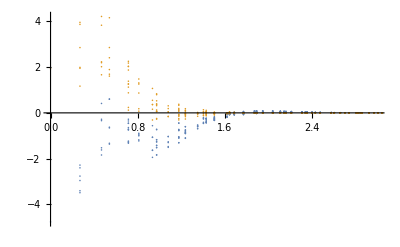

```mathematica
ListPlot[{rtotE1,rtotE2},PlotRange->{{0,3},All}]
```

```mathematica
Total[rtotE1[[1;;1000]]]+Total[rtotE2[[1;;1000]]]
```

{5977.65,-33.6158}

```mathematica
Total Energy of both layers centered on each atom
```

```mathematica
distance=Norm[totE1[[7120,{1,2}]]-totE2[[7120,{1,2}]]];
carretotE1=ArrayReshape[totE1,{100,100,3}];
carretotE2=ArrayReshape[totE2,{100,100,3}];
totE=carretotE1;
```

```mathematica
For[i=3,i<97,i++,
For[j=3,j<97,j++,
u=carretotE1[[i,j,{1,2}]];
Etria=0
For[k=-1,k<2,k++,
For[l=-1,l<2,l++,
v=carretotE2[[i+k,j+l,{1,2}]];
If[Abs[Norm[u-v]-distance]<0.00001,
totE[[i,j,3]]=totE[[i,j,3]]+carretotE2[[i+k,j+l,3]]/3.0;]
];];];];
```

```mathematica
totEformat=ArrayReshape[totE,{100*100,3}];
```

```mathematica
rhototE=Sort[Table[{Norm[totEformat[[i,{1,2}]]-totEformat[[7120,{1,2}]]],totEformat[[i,3]]},{i,1,100*100}],#1[[1]]<#2[[1]]&];
```

```mathematica
end=100*99;i=2;
avetotE={{rhototE[[1,1]],rhototE[[1,2]],0}};
While[i<end+1,
n=0;j=0;
While[Abs[rhototE[[i+j,1]]-rhototE[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[avetotE,{rhototE[[i,1]],Mean[rhototE[[i;;i+n-1,2]]],Sqrt[Total[(Mean[rhototE[[i;;i+n-1,2]]]-rhototE[[i;;i+n-1,2]])^2]/n]}];i=i+n,AppendTo[avetotE,{rhototE[[i,1]],rhototE[[i,2]],0}];i=i+1];
]
```

```mathematica
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Etot/profile_totE.dat",avetotE,"Table"];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Etot/totE.dat",totEformat,"Table"];
```

```mathematica
end=100*99;i=4;
sumrtotE={{rhototE[[1,1]],Total[rhototE[[1;;3,2]]]}};
While[i<end+1,
n=0;j=0;
While[Abs[rhototE[[i+j,1]]-rhototE[[i,1]]]<0.0000001,n=n+1;j++];
If[n≠1,AppendTo[sumrtotE,{rhototE[[i,1]],Total[rhototE[[1;;i+n-1,2]]]}];i=i+n,AppendTo[sumrtotE,{rhototE[[i,1]],Total[rhototE[[1;;i,2]]]}];i=i+1];
]
```

```mathematica
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/3.5T/2DM/profile/profile_Etot/sumtotE.dat",sumrtotE,"Table"];
```

```mathematica
plotAVEtotE=ListPlot[avetotE,PlotRange->{{-0.05,4},All},PlotMarkers->{Automatic,Large},PlotStyle->Black,AspectRatio->1,FrameTicks->{{Flatten[{Table[{j,j,{0.02,0}},{j,-1,4,0.5}],Table[{j,,{0.01,0}},{j,-1,4,0.1}]},1],Flatten[{Table[{j,,{0.02,0}},{j,-1,4,0.5}],Table[{j,,{0.01,0}},{j,-1,4,0.1}]},1]},{Flatten[{Table[{j,j,{0.02,0}},{j,0,4,1}],Table[{j,,{0.01,0}},{j,0,4,0.2}]},1],Flatten[{Table[{j,,{0.02,0}},{j,0,4,1}],Table[{j,,{0.01,0}},{j,0,4,0.2}]},1]}},ColorFunction->ColorData[{"Temperature",{-2,2}}],ColorFunctionScaling->False,Filling->Axis,Joined->True,FrameLabel->{Style["r (nm)",FontSize->50],Style["Energy relative FM state (meV/atom)",FontSize->40]},BaseStyle->{FontSize->26},LabelStyle->Directive[Bold,Thick,Large],Frame->True,FrameStyle->Directive[Thickness[0.005],FontSize->50],ImageSize->1000,ImagePadding->{{300,100},{100,100}}];
Export["/Users/Bertrand/Dropbox/MC/RhPd_2Fe_Ir111/coeff-september2014/RhPd2Fe2Ir/final-fit/sans-dip/isolated-Sk/4T/profile/AVEEtot-recenter.pdf",plotAVEtotE,"pdf"];
```